FittedModel[0.124842-0.0290542 x]

{{x→4.29687-34.4184 y}}

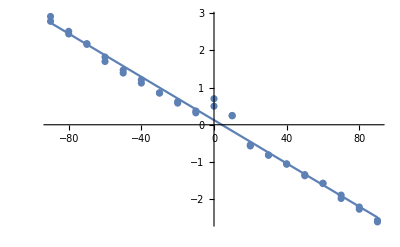

```mathematica
data={
{0,2.91,2.78},{10,2.51,2.44},{20,2.16,2.18},{30,1.82,1.7},{40,1.47,1.39},{50,1.21,1.12},{60,0.86,0.85},{70,0.622,0.582},{80,0.37,0.32},{90,0.5,0.7},{100,0.24,0.25},{110,-0.54,-0.57},{120,-0.82,-0.81},{130,-1.05,-1.06},{140,-1.34,-1.37},{150,-1.58,-1.57},{160,-1.98,-1.89},{170,-2.27,-2.21},{180,-2.61,-2.57}
};
data[[All,1]]=data[[All,1]]-90;
(*data[[All,{2, 3}]]=data[[All,{2, 3}]]-2.2;*)

separated=Join[data[[All, {1, 2}]], data[[All, {1,3}]]];

angleModel=LinearModelFit[separated, x, x]
inverseModel=Solve[angleModel[x]==y, x]//Expand

Show[
ListPlot[separated],
Plot[angleModel[θ], {θ, Min[data[[All, 1]]], Max[data[[All, 1]]]}]
]
```